```mathematica
ClearAll;
Off[NIntegrate::ncvb]
Off[NIntegrate::precw]
Off[NIntegrate::slwcon]
Off[Root::npoly]
SetDirectory[NotebookDirectory[]];
On[Assert]
```

## Set Parameters

```mathematica
wkpc = 20; (*working precision*)
MaxOrder = 30; (*highest order of basis used *)
xdetector = 0.3 (*cm*);
m=7/2;
mh = 7/2;
ξmaxn3 = 1.119935;   (*Subscript[ξ, max] for n = 3*)
ξmaxn0 = 1.231173;  (*Subscript[ξ, max] for n = 0*)
ξmaxn72 = 1.1110443;  (*Subscript[ξ, max] for n = 7/2*)
T0val = 0.4;
ρ0val = 0.1134;
ZZ =4.5;
κ0val = 0.088*ZZ^2*0.4^(-7/2)* ρ0val;
cv0val = 10;
stdDrive = 0.1 * T0val;
stdDensity = 0.1 * ρ0val;
NPn = 12;
NHe=12;
tval = 0.6
pval = 0.1;
Nevalpoints = 50;
omegaval =  2 Sqrt[(2a c)]/Sqrt[3(n+4)]/.{n->mh, a-> 0.01372, c -> 299.98 };
omegavaln0 =  2 Sqrt[(2a c)]/Sqrt[3(n+4)]/.{n->0, a-> 0.01372, c -> 299.98 };
omegafunc[a_,c_, n_]:= 2 Sqrt[(2a c)]/Sqrt[3(n+4)];
δH = 0.5;
DrivePars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval* T0val, a2->0, a3->0, a4->0,ω->omegaval};
DriveParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->stdDrive , a2->0, a3->0, a4->0,ω->omegaval};
DensityPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0.0 , a2->0, a3->0.1*ρ0val, a4->0,ω->omegaval};
BothPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval*T0val, a2->0, a3->pval*ρ0val, a4->0,ω->omegaval};
BothParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->stdDrive, a2->0, a3->stdDensity, a4->0,ω->omegaval, n->mh};
DensityParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0.0 , a2->0, a3->stdDensity, a4->0,ω->omegaval, n->mh};
transfer ={Subscript[a, 1]->a1, Subscript[a, 3]->a3,Subscript[a, 4]->a4,Subscript[a, 2]->a2, ρ̄->ρ0, OverBar[Subscript[c, v]]->cv, κ̄->κ0, T̄->T0, n->mh, ξ->ξmaxn72, ω->omegaval};
AllPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval* T0val, a2->pval*κ0val, a3->pval*ρ0val, a4->pval*cv0val,ω->omegaval};
TargetPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0, a2->pval*κ0val, a3->pval*ρ0val, a4->pval*cv0val,ω->omegaval};
```

0.6

## Some lists

```mathematica
FactorialList = Table[Factorial[j],{j,0,NHe}];
LegendreList = Table[1/(2 j+ 1),{j,0, NPn}];
```

## Useful functions

```mathematica
T0funcU[x_, pars_]:=( T0 + a1 x)/.pars
analyticProfileDriveUncertainty[x_,t_, pars_] := 1/2 NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0, 0, 0],{xx1, -1,1}, WorkingPrecision->14]
ξfunc[AA_, x_, t_] := AA x/Sqrt[t] 
IntegrandFunc2[x_,t_,pars_, x1_, x2_, x3_, x4_] := Tsol2[ξfunc[AAfunc[pars, x1, x2, x3, x4],x, t]] * T0funcU[x1, pars]
RMSE[data1_, data2_]:= Sqrt[Mean[(data1-data2)^2]]
AAfunc[ pars_,x1_, x2_, x3_, x4_]:= Sqrt[((κ0 + a2 x2)   (cv + a4 x4)( ρ0 + a3 x3)^2)/(T0 + a1 x1)^(mh)]  / ω/.pars;
tempNthMomentPn[x_,t_, pars_, k_] := 1/16 NIntegrate[IntegrandFunc2[x,t,pars, xx1, xx2, xx3, xx4]^k,{xx1,-1,1},{xx2, -1,1},{xx3, -1,1},{xx4,-1,1}, PrecisionGoal->12]
tempNthMomentHe[x_,t_, pars_, k_] := 1/(4 Pi^2)NIntegrate[IntegrandFunc2[x,t,pars, xx1, xx2, xx3, xx4]^k Exp[-xx1^2/2]Exp[-xx2^2/2]Exp[-xx3^2/2]Exp[-xx4^2/2],{xx1,-∞,∞},{xx2, -∞,∞},{xx3, -∞,∞},{xx4,-∞,∞}, WorkingPrecision->14]
analyticprofileDriveHe[x_,t_, pars_] := 1/Sqrt[2 Pi] NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0, 0, 0] Exp[-xx1^2/2],{xx1,-∞,∞}, WorkingPrecision->14]
sobol[SAMPLES_, dim_]:=BlockRandom[SeedRandom[Method->{"MKL",Method->{"Sobol","Dimension"->dim}}];
RandomReal[1,{SAMPLES,dim}]];
Basis[n_,x_] := LegendreP[n,x]
HBasis[nnn_, x_] := FullSimplify[(-1)^(nnn) Exp[xx^2/2] D[Exp[-xx^2/2],{xx,nnn}]/.xx->x];
BreakoutTime[θ1_, θ2_, θ3_, θ4_, pars_, xdet_]:=  (xdet^2/(ξ^2 ω^2))(T̄ + a1 θ1)^(-(n))(κ̄ + a2_ θ2)^1(ρ̄ + a3 θ3)^2(OverBar[Subscript[c, v]] + a4_ θ4)^1/.{T̄->T0,ρ̄->ρ0,OverBar[Subscript[c, v]] ->cv,κ̄ ->κ0 }/.pars
(*functions to calculate expansion of the breakout time*)
g1func[x_, pars_,n_]:= 1/(ξ^2 ω^2) (T0 + a1 x)^(-n)/.pars;
g2func[x_,pars_]:= (κ0 + a2 x)^(1)/.pars;
g3func[x_,pars_]:= (ρ0 + a3 x)^(2)/.pars;
g4func[x_,pars_] := (cv + a4 x)^(1)/.pars 
G1func[n_,pars_,nn_, bound_]:= (2n + 1)/2 NIntegrate[g1func[ x,pars,nn] Basis[n,x], {x, -bound,bound}, WorkingPrecision->2*wkpc, AccuracyGoal->18]
G2func[n_,pars_, bound_]:=  (2n + 1)/2 NIntegrate[g2func[x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
G3func[n_,pars_, bound_]:= (2n + 1)/2 NIntegrate[g3func[x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
G4func[n_,pars_, bound_]:=  (2n + 1)/2 NIntegrate[g4func[ x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
HG1func[n_,pars_,nn_, bound_]:=1/(Sqrt[2 Pi] Factorial[n])NIntegrate[(g1func[ z,pars,nn]) HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, (*Exclusions->z==  N[-T0/a1/.pars]*)WorkingPrecision->wkpc, AccuracyGoal->15]
HG2func[n_,pars_, bound_]:= 1/(Sqrt[2 Pi] Factorial[n])NIntegrate[g2func[ z,pars] HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
HG3func[n_,pars_, bound_]:=1/(Sqrt[2 Pi] Factorial[n]) NIntegrate[( g3func[ z,pars]) HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
HG4func[n_,pars_, bound_]:= 1/(Sqrt[2 Pi] Factorial[n])NIntegrate[g4func[z,pars] HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
g1coeffs[M_,pars_,nn_,b_] := Table[G1func[n,pars,nn, b],{n,0,M}]
g2coeffs[M_,pars_, b_] := Table[G2func[n,pars, b],{n,0,M}]
g3coeffs[M_,pars_, b_] := Table[G3func[n,pars, b],{n,0,M}]
g4coeffs[M_,pars_, b_] := Table[G4func[n,pars, b],{n,0,M}]
h1coeffs[M_,pars_,nn_,b_] := Table[HG1func[ni, pars,nn, b],{ni,0,M}]
h2coeffs[M_,pars_, b_] := Table[HG2func[ni,pars, b],{ni,0,M}]
h3coeffs[M_,pars_, b_] := Table[HG3func[ni,pars, b],{ni,0,M}]
h4coeffs[M_,pars_, b_] := Table[HG4func[ni,pars, b],{ni,0,M}]
MakeCoeffsG[NN_, pars_, m_]:= {g1coeffs[NN,pars,m,1], g2coeffs[NN, pars,1],g3coeffs[NN, pars,1],g4coeffs[NN, pars,1] }
MakeCoeffsH[NN_, pars_, m_]:= {h1coeffs[NN,pars,m,1], h2coeffs[NN, pars,1],h3coeffs[NN, pars,1],h4coeffs[NN, pars,1] }
BasisList = Table[Basis[j,x],{j,0,MaxOrder}];
BasisListF[n_,xx_] := BasisList[[n+1]]/.x->xx
expansion[x1_,x2_,x3_,x4_, coeffs_, NN_]:= Total[ParallelTable[coeffs[[1]][[n]]Basis[n-1,x1],{n,1,NN+1}]]*Total[Table[coeffs[[2]][[n]]Basis[n-1,x2],{n,1,NN+1}]]*Total[Table[coeffs[[3]][[n]]Basis[n-1,x3],{n,1,NN+1}]]*Total[Table[coeffs[[4]][[n]]Basis[n-1,x4],{n,1,NN+1}]]
HBasisList = Table[HBasis[j,x],{j,0,MaxOrder}];
HBasisListF[n_,xx_] := HBasisList[[n+1]]/.x->xx
Hexpansion[x1_,x2_,x3_,x4_, coeffs_, NN_]:= Total[Table[coeffs[[1]][[n]]HBasisListF[n-1,x1],{n,1,NN+1}]]*Total[Table[coeffs[[2]][[n]]HBasisListF[n-1,x2],{n,1,NN+1}]]*Total[Table[coeffs[[3]][[n]]HBasisListF[n-1,x3],{n,1,NN+1}]]*Total[Table[coeffs[[4]][[n]]HBasisListF[n-1,x4],{n,1,NN+1}]]
(*Functions to calculate moments of the 1d expansions*) 
MakeExpPn[coeffs_] := coeffs[[1]][[1]]coeffs[[2]][[1]]coeffs[[3]][[1]]coeffs[[4]][[1]]*xdetector^2
MakeExpHe[coeffs_] := coeffs[[1]][[1]]coeffs[[2]][[1]]coeffs[[3]][[1]]coeffs[[4]][[1]]*xdetector^2
MakeSecondMomentHe[nn_, coeffs_]:=xdetector^4*Total[coeffs[[1]][[1;;nn]]^2 FactorialList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2FactorialList[[1;;nn]]]
MakeVarPn[nn_,coeffs_]:=xdetector^4*Total[coeffs[[1]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2LegendreList[[1;;nn]]] - MakeExpPn[coeffs]^2
MakeVarHe[nn_,coeffs_]:= xdetector^4*Total[coeffs[[1]][[1;;nn]]^2 FactorialList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2FactorialList[[1;;nn]]] - (MakeExpHe[coeffs])^2
MakeSkewPn[nn_, coeffs_]:= (1/16 xdetector^6ThirdMoment[nn, TripleProdLeg, coeffs[[1]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[2]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[3]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[4]][[1;;nn]]] - 3 MakeExpPn[coeffs]MakeVarPn[nn, coeffs] -MakeExpPn[coeffs]^3) /(MakeVarPn[nn, coeffs]^(3/2))
MakeSkewHe[nn_, coeffs_]:= ( xdetector^6ThirdMoment[nn, TripleProdHe, coeffs[[1]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[2]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[3]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[4]][[1;;nn]]] - 3 MakeExpHe[coeffs]MakeVarHe[nn, coeffs] -MakeExpHe[coeffs]^3) /(MakeVarHe[nn, coeffs]^(3/2))
MakeKurtPn[nn_, coeffs_]:= (1/16 xdetector^8FourthMoment[nn, QuadrupleProdLeg, coeffs[[1]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[2]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[3]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[4]][[1;;nn]]] - 6(MakeVarPn[nn,coeffs]+MakeExpPn[coeffs]^2)MakeExpPn[coeffs]^2 - 3 MakeExpPn[coeffs]^4)/ MakeVarPn[nn, coeffs]^2
MakeKurtHe[nn_, coeffs_]:= (xdetector^8FourthMoment[nn, QuadrupleProdHe, coeffs[[1]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[2]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[3]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[4]][[1;;nn]]] - 6(MakeSecondMomentHe[nn,coeffs])MakeExpHe[coeffs]^2 - 3 MakeExpHe[coeffs]^4)/ MakeVarHe[nn, coeffs]^2
ThirdMoment[nn_,AAA_, coeffs_]:= Total[Total[Total[Table[AAA[[i]][[j]][[k]]coeffs[[i]]coeffs[[j]]coeffs[[k]],{i,1,nn}, {j,1,nn},{k,1,nn}]]]]
(*ThirdMoment[nn_,AAA_, coeffs_]:= Integrate[Total[Total[Total[]]],{x,-1,1}]*)
FourthMoment[nn_,AAA_, coeffs_]:=Total[ Total[Total[Total[Table[AAA[[i]][[j]][[k]][[n]]coeffs[[i]]coeffs[[j]]coeffs[[k]]coeffs[[n]],{i,1,nn}, {j,1,nn},{k,1,nn},{n,1,nn}]]]]]
```

## Expensive tensors that can be loaded

```mathematica
TripleProdHeFunc[i_,j_,k_]:= If[(i!= 0 && j!= 0 && k != 0) && j+k<i || Abs[j-k]>i || (EvenQ[j+k]&& OddQ[i ]|| OddQ[j+k]&&EvenQ[i]),0, 1/Sqrt[2 Pi] Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]Exp[-x^2/2],{x,-∞,∞}]]
QuadrupleProdHeFunc[i_,j_,k_,m_]:= If[(i!= 0 && j!= 0 && k != 0) && j+k<i +m|| Abs[j-k]>i+m || (EvenQ[j+k]&& OddQ[i+m ]|| OddQ[j+k]&&EvenQ[i+m]),0, 1/Sqrt[2 Pi] Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]HBasis[m,x]Exp[-x^2/2],{x,-∞,∞}]]
```

```mathematica
(*TripleProdLeg =ParallelTable[ Integrate[Basis[i,x]Basis[j,x]Basis[k,x],{x,-1,1}],{i,0,NPn},{j,0,NPn},{k,0,NPn}];
TripleProdHe = ParallelTable[TripleProdHeFunc[i,j,k],{i,0,NHe},{j,0,NHe}, {k,0,NHe}];*)
```

```mathematica
(*QuadrupleProdLeg =ParallelTable[ Integrate[Basis[i,x]Basis[j,x]Basis[k,x]Basis[n,x],{x,-1,1}],{i,0,NPn},{j,0,NPn},{k,0,NPn},{n,0,NPn}];*)
```

```mathematica
(*QuadrupleProdHe =ParallelTable[QuadrupleProdHeFunc[i,j,k,n],{i,0,NHe},{j,0,NHe},{k,0,NHe},{n,0,NHe}];*)
```

```mathematica
(*Export["triple_prod_leg.hdf",TripleProdLeg];
Export["triple_prod_he.hdf",TripleProdHe];
Export["quadruple_prod_leg.hdf",QuadrupleProdLeg];
Export["quadruple_prod_he.hdf",QuadrupleProdHe];*)
TripleProdLeg2=Rationalize[Import["triple_prod_leg.hdf",{"Datasets","Dataset1"}]];
TripleProdHe2=Rationalize[Import["triple_prod_he.hdf",{"Datasets","Dataset1"}]];
QuadrupleProdLeg2=Rationalize[Import["quadruple_prod_leg.hdf",{"Datasets","Dataset1"}]];
QuadrupleProdHe2=Rationalize[Import["quadruple_prod_he.hdf",{"Datasets","Dataset1"}]];
Assert[Total[Total[Total[TripleProdLeg2-TripleProdLeg ]]]==0]
Assert[Total[Total[Total[TripleProdHe2-TripleProdHe ]]]==0]
Assert[Total[Total[Total[Total[QuadrupleProdLeg2-QuadrupleProdLeg ]]]]==0]
Assert[Total[Total[Total[Total[QuadrupleProdHe2-QuadrupleProdHe ]]]]==0]
TripleProdLeg = TripleProdLeg2;
TripleProdHe = TripleProdHe2;
QuadrupleProdLeg = QuadrupleProdLeg2;
QuadrupleProdHe = QuadrupleProdHe2;
```

```mathematica
"
```

## Analytic solutions

```mathematica
DriveBkoutnthMomentPn[n2_]:= 1/2((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2)^n2 ((-a1^2+T0^2)^(-mh n2) (-(-a1+T0)^(mh n2) (a1+T0)+(-a1+T0) (a1+T0)^(mh n2)))/(a1 (-1+mh n2)) (* nth moment of a URV drive uncertainty*)
AllBkoutnthMomentPn[n2_]:=-((((xdetector^2 (T0-Subscript[a, 1])^-n)/(ξ^2 ω^2))^n2 (-T0+Subscript[a, 1])+(T0+Subscript[a, 1]) ((xdetector^2 (T0+Subscript[a, 1])^-n)/(ξ^2 ω^2))^n2) (-(κ0-Subscript[a, 2])^(1+n2)+(κ0+Subscript[a, 2])^(1+n2)) (-(ρ0-Subscript[a, 3])^(1+2 n2)+(ρ0+Subscript[a, 3])^(1+2 n2)) (-(cv-Subscript[a, 4])^(1+n2)+(cv+Subscript[a, 4])^(1+n2)))/(16 (1+n2)^2 (1+2 n2) (-1+n n2) Subscript[a, 1] Subscript[a, 2] Subscript[a, 3] Subscript[a, 4]) (* nth moment of a URV all uncertain*)
DriveBkoutnthMomentHe[n2_, pars_]:=1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-∞,∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->10, Method->"GlobalAdaptive"]  (* nth moment of a NRV drive uncertain*)
DriveBkoutnthMomentHeSing[n2_, pars_, δH_]:=1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-(-δH+(T0/a1/.pars)),-δH+(T0/a1/.DrivePars)},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"]   +1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-∞,-δH-(T0/a1/.DrivePars)},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"]   +1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,δH+(T0/a1/.DrivePars),∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"] (* nth moment of a URV all uncertain, tries to avoid the singularity*)
HeBreakoutIntegrand[pars_,θ1_,θ2_,θ3_,θ4_,n2_]:=1/Sqrt[2 Pi]^4((( ρ0+Subscript[a, 3] θ3)^2 (cv+Subscript[a, 4] θ4)(κ0+Subscript[a, 2] θ2))/(ξ^2ω^2)(Subscript[a, 1] θ1+T0)^(-n )xdetector^2/.transfer/.pars)^n2 Exp[-θ1^2/2]Exp[-θ2^2/2]Exp[-θ3^2/2]Exp[-θ4^2/2]/.transfer/.pars/.n->mh
AllBkoutnthMomentHe[n2_, pars_]:=NIntegrate[HeBreakoutIntegrand[pars,Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],n2],{Subscript[θ, 1],-∞,∞},{Subscript[θ, 2],-∞,∞},{Subscript[θ, 3],-∞,∞},{Subscript[θ, 4],-∞,∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->10, Method->"GlobalAdaptive"]  
AllBkoutnthMomentHeSing[n2_, pars_, δH_]:=NIntegrate[HeBreakoutIntegrand[pars,Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],n2],{Subscript[θ, 1],-(-δH+(T0/a1/.pars)),-δH+(T0/a1/.pars)},{Subscript[θ, 2],-∞,∞},{Subscript[θ, 3],-∞,∞},{Subscript[θ, 4],-∞,∞},WorkingPrecision->20, AccuracyGoal->12, PrecisionGoal->12, Method->"GlobalAdaptive"]  
(*These calculate the moment based statistics of Subscript[t, b] for uncertain drive*)
 varExact = (DriveBkoutnthMomentPn[2] - DriveBkoutnthMomentPn[1]^2)/.DrivePars;
varExactHe = (DriveBkoutnthMomentHe[2, DrivePars] - DriveBkoutnthMomentHe[1, DrivePars]^2);
skewExact = (DriveBkoutnthMomentPn[3] - 3 DriveBkoutnthMomentPn[1]varExact - DriveBkoutnthMomentPn[1]^3)/varExact^(3/2)/.DrivePars;
skewExactHe = (DriveBkoutnthMomentHeSing[3,DrivePars,δH] - 3 DriveBkoutnthMomentHe[1, DrivePars]varExactHe - DriveBkoutnthMomentHe[1, DrivePars]^3)/varExactHe^(3/2);
kurtExact = (DriveBkoutnthMomentPn[4] - 6 DriveBkoutnthMomentPn[2]DriveBkoutnthMomentPn[1]^2 -3 DriveBkoutnthMomentPn[1]^4)/varExact^(2)/.DrivePars;
kurtExactHe = 1/varExactHe^(2)(DriveBkoutnthMomentHeSing[4,DrivePars,δH] - 6 DriveBkoutnthMomentHe[2, DrivePars]DriveBkoutnthMomentHe[1, DrivePars]^2 -3 DriveBkoutnthMomentHe[1,DrivePars]^4)/.DrivePars;
(*These calculate the moment based statistics of Subscript[t, b] for all parameters uncertain *)
varExactAll = (AllBkoutnthMomentPn[2] - AllBkoutnthMomentPn[1]^2)/.transfer/.AllPars;
varExactHeAll = (AllBkoutnthMomentHe[2, AllPars] - AllBkoutnthMomentHe[1, AllPars]^2);
skewExactAll = (AllBkoutnthMomentPn[3] - 3 AllBkoutnthMomentPn[1]varExactAll - AllBkoutnthMomentPn[1]^3)/varExactAll^(3/2)/.transfer/.AllPars;

kurtExactAll = (AllBkoutnthMomentPn[4] - 6 AllBkoutnthMomentPn[2]AllBkoutnthMomentPn[1]^2 -3 AllBkoutnthMomentPn[1]^4)/varExactAll^(2)/.transfer/.AllPars;
δH = 0.5;
firstmom =AllBkoutnthMomentHeSing[1, AllPars, δH];
skewExactHeAll = (AllBkoutnthMomentHeSing[3,AllPars, δH] - 3firstmom varExactHeAll - firstmom^3)/varExactHeAll^(3/2);
kurtExactHeAll = 1/varExactHeAll^(2)(AllBkoutnthMomentHeSing[4,AllPars, δH] - 6AllBkoutnthMomentHe[2, AllPars]firstmom^2 -3 firstmom^4)/.AllPars;
```

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

## Breakout time convergence

```mathematica
(*calculate 1d coefficients and export to python*)
NN = 14; (*order of the basis *)
drivecoeffs = MakeCoeffsG[NN, DrivePars, mh];
targetcoeffs = MakeCoeffsG[NN, TargetPars, mh];
bothcoeffs = MakeCoeffsG[NN, BothPars, mh];
allcoeffs = MakeCoeffsG[NN, AllPars, mh];
drivecoeffsH = MakeCoeffsH[NN, DrivePars, mh];
targetcoeffsH = MakeCoeffsH[NN, TargetPars, mh];
bothcoeffsH = MakeCoeffsH[NN, BothPars, mh];
allcoeffsH = MakeCoeffsH[NN, AllPars, mh];
Export["drivecoeffs.csv", drivecoeffs];
Export["targetcoeffs.csv", targetcoeffs];
Export["allcoeffs.csv", allcoeffs];
Export["drivecoeffs_he.csv", Re[drivecoeffsH]];
Export["targetcoeffs_he.csv", Re[targetcoeffsH]];
Export["allcoeffs_he.csv", Re[allcoeffsH]];
```

$Aborted

$Aborted

```mathematica
(*Drive uncertainty*)
```

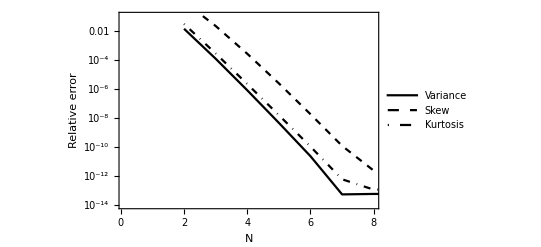

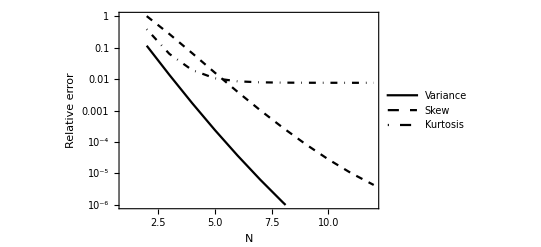

```mathematica
ERR = Table[0, {k,0,3},{j,NPn-1}];
ERRHe = Table[0, {k,0,3},{j,NHe-1}];
For[nn = 2, nn<=NPn, nn++,
vartest = MakeVarPn[nn,drivecoeffs[[;;]]];
skewtest = MakeSkewPn[nn, drivecoeffs[[;;]]];
kurttest = MakeKurtPn[nn,drivecoeffs[[;;]]] ;
ERR[[1]][[nn-1]] = {nn,Abs[(vartest - varExact)]/varExact};
ERR[[2]][[nn-1]]={nn,Abs[(skewtest - skewExact)]/skewExact};
ERR[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExact)]/Abs[kurtExact] };
]
For[nn = 2, nn<=NHe, nn++,
vartest = MakeVarHe[nn,drivecoeffsH[[;;]]];
skewtest = MakeSkewHe[nn, drivecoeffsH[[;;]]];
kurttest = MakeKurtHe[nn,drivecoeffsH[[;;]]] ;
ERRHe[[1]][[nn-1]] = {nn,Abs[(vartest - varExactHe)]/Abs[varExactHe]};
ERRHe[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactHe)]/Abs[skewExactHe]};
ERRHe[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactHe)]/Abs[kurtExactHe] };
]
styles=Flatten@Table[{Directive[color],Directive[Dashed,color, Thick],Directive[DotDashed,color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];
drivePnConvergence = ListLogPlot[{ERR[[1]], ERR[[2]], ERR[[3]]}, Joined->True, PlotRange->{{0.1, NPn-4},{10^(-14),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
driveHeConvergence = ListLogPlot[{ERRHe[[1]], ERRHe[[2]], ERRHe[[3]]}, Joined->True, PlotRange->{{1, 12},{10^(-6),1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
```

```mathematica
(*All uncertainty*)
```

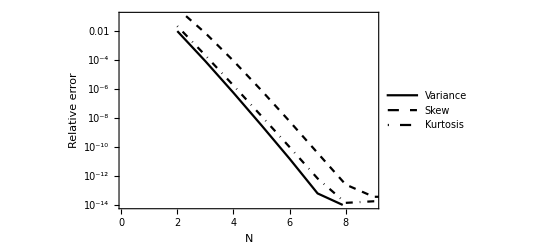

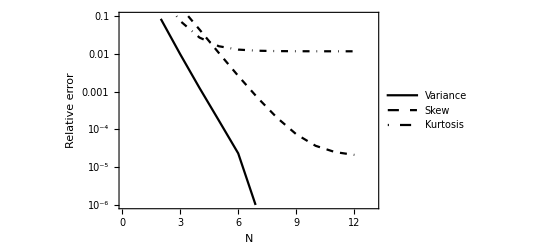

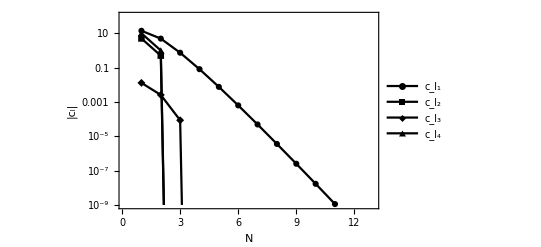

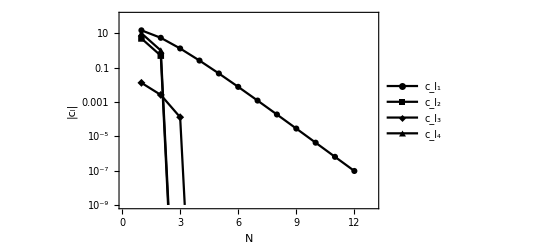

```mathematica
ERRAll = Table[0, {k,0,3},{j,NPn-1}];
ERRHeAll = Table[0, {k,0,3},{j,NHe-1}];
For[nn = 2, nn<=NPn, nn++,
vartest = MakeVarPn[nn,allcoeffs[[;;]]];
skewtest = MakeSkewPn[nn, allcoeffs[[;;]]];
kurttest = MakeKurtPn[nn,allcoeffs[[;;]]] ;
ERRAll[[1]][[nn-1]] = {nn,Abs[(vartest - varExactAll)]/varExactAll};
ERRAll[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactAll)]/skewExactAll};
ERRAll[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactAll)]/Abs[kurtExactAll] };
]
For[nn = 2, nn<=NHe, nn++,
vartest = MakeVarHe[nn,allcoeffsH[[;;]]];
skewtest = MakeSkewHe[nn, allcoeffsH[[;;]]];
kurttest = MakeKurtHe[nn,allcoeffsH[[;;]]] ;
ERRHeAll[[1]][[nn-1]] = {nn,Abs[(vartest - varExactHeAll)]/varExactHeAll};
ERRHeAll[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactHeAll)]/skewExactHeAll};
ERRHeAll[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactHeAll)]/Abs[kurtExactHeAll] };
]
AllPnConvergence = ListLogPlot[{ERRAll[[1]], ERRAll[[2]], ERRAll[[3]]}, Joined->True, PlotRange->{{0.1, NPn-3},{10^(-14),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
AllHeConvergence = ListLogPlot[{Re[ERRHeAll[[1]][[1;;6]]], ERRHeAll[[2]], ERRHeAll[[3]]}, Joined->True, PlotRange->{{0.1, NHe+1},{10^(-6),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
styles2=Flatten@Table[{Directive[color],Directive[color],Directive[color],Directive[color]},{color,{Black,Gray}} ];
CoeffsAllPnPlot = ListLogPlot[{ Table[{j, Abs[allcoeffs[[1]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffs[[2]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffs[[3]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffs[[4]][[j]]]},{j,0,NPn}]},Joined->True, PlotStyle->styles2,Frame->{True, True, False, False},PlotMarkers->Automatic, PlotRange->{{0.1, NPn+1},{10^(-9),100}}, FrameLabel->{Style["N", Large],Style["|c_l|", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"c_l_1","c_l_2", "c_l_3", "c_l_4"}]
CoeffsAllHePlot = ListLogPlot[{ Table[{j, Abs[allcoeffsH[[1]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsH[[2]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsH[[3]][[j]]]},{j,0,NHe+1}], Table[{j, Abs[allcoeffsH[[4]][[j]]]},{j,0,NPn}]},Joined->True, PlotStyle->styles2,Frame->{True, True, False, False},PlotMarkers->Automatic, PlotRange->{{0.1, NPn+1},{10^(-9),100}}, FrameLabel->{Style["N", Large],Style["|c_l|", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"c_l_1","c_l_2", "c_l_3", "c_l_4"}]
(*Export[ "UQ_plots/drivePnConverge.pdf",drivePnConvergence]*)
(*Export[ "UQ_plots/driveHeConverge.pdf",driveHeConvergence]*)
(*Export[ "UQ_plots/AllPnConverge_10.pdf",AllPnConvergence]*)
(*Export[ "UQ_plots/AllHeConverge.pdf",AllHeConvergence]*)
(*Export["UQ_plots/CoeffsAllUncertainPn_10.pdf",CoeffsAllPnPlot]*)
(*Export["UQ_plots/CoeffsAllUncertainHe_10.pdf",CoeffsAllHePlot]*)
```

```mathematica
Print["Expected Pn ", MakeExpPn[allcoeffs]]
Print["Expected He ", MakeExpHe[allcoeffsH]]
```

Expected Pn 0.813972

Expected He 0.867198

## Histogram plots of breakout time

```mathematica
(*Load results from python*)
```

```mathematica
heresults =Import["he_samples.hdf5", "results"];
pnresults =Import["pn_samples.hdf5", "results"];
Hsamples = heresults[[1]];
Hdensitysamples= heresults[[2]];
Hallsamples = heresults[[3]];
samples = pnresults[[1]];
densitysamples= pnresults[[2]];
allsamples = pnresults[[3]];
```

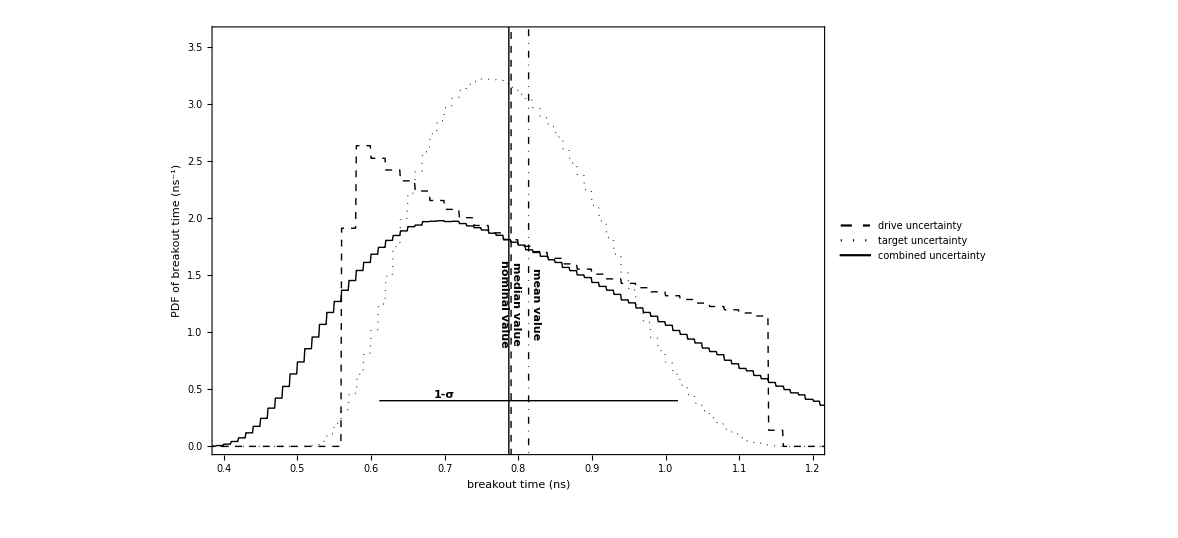

```mathematica
xmin = Min[allsamples];
xmax = Max[allsamples];
mean = Mean[allsamples];
std = Sqrt[Variance[allsamples]];
median = Median[allsamples];
nominal = expansion[0,0,0,0, allcoeffs, NN] * xdetector^2;
lineStyle={Thick,Red,Dashed};
maxy = 100;
line1=Line[{{median,-20},{median,maxy}}];
line2 = Line[{{mean,-20},{mean,maxy}}];
line3 = Line[{{nominal,-20},{nominal,maxy}}];
(*line4 = Line[{{AnalyticBreakout,-20},{AnalyticBreakout,maxy}}];*)
line5 = Line[{{mean- std, 0.4}, {mean+std, 0.4}}];
line6 = Line[{{mean - std, -20}, {mean-std, 20}}];
𝒟= HistogramDistribution[samples];
𝒟2= HistogramDistribution[densitysamples, {0.01}];
(*𝒟3= HistogramDistribution[combinedsamples, {0.01}];*)
(*𝒟4 =  HistogramDistribution[DirectSampleBothParsU, {0.01}];*)
𝒟5 =  HistogramDistribution[allsamples, {0.01}];
styles3=Flatten@Table[{Directive[Dashed,color, Thick],Directive[Dotted,color, Thick],Directive[color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];
shiftδ = 10^{-8}*0;
(*PDF PN*)
( DiscretePlot[{ #[𝒟,x]+shiftδ,#[𝒟2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[𝒟5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,3.6}},Epilog->{Black, line1, Text[Rotate[Style["median value",Black,Bold, Medium],-90 Degree],{median + .01,1.25}],Black,DotDashed,line2,Text[Rotate[Style["mean value",Black,Bold, Medium],-90 Degree],{mean+.01,1.25}],Black,Dashed, line3, Text[Rotate[Style["nominal value",Black,Bold, Medium],-90 Degree],{nominal-.01,1.25}], Black,Dashing[None], line5, Text[Style["1-σ",Black,Bold, Medium],{0.7,0.45}]}, PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["PDF of breakout time (ns^-1)", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{PDF})[[1]]
```

```mathematica
𝒟5N =  HistogramDistribution[allsamples, {0.00001}];
percentilelist = {.20,.40,.50,.60,.80};
twentieth = InverseCDF[𝒟5N,0.2];
eightieth= InverseCDF[𝒟5N,0.8];
fiftieth = InverseCDF[𝒟5N,0.5];
nominalcdf = CDF[𝒟5N,nominal];
meancdf = CDF[𝒟5N,mean];
For[n =1,n<= 5, n++,Print[NumberForm[InverseCDF[𝒟5N,percentilelist[[n]]],6]," ", percentilelist[[n]]," percentile"]]
```

0.63078 0.2 percentile

0.733865 0.4 percentile

0.78712 0.5 percentile

0.845111 0.6 percentile

0.989323 0.8 percentile

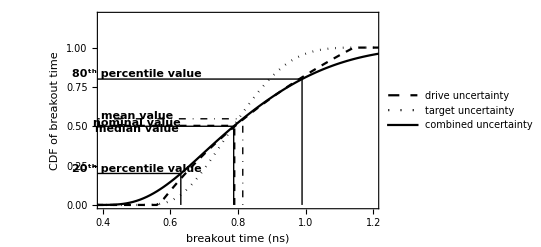

```mathematica
line7 = Line[{{0, 0.5}, {fiftieth, 0.5}}];
line8 = Line[{{fiftieth, 0.0}, {fiftieth, 0.5}}];
line9 = Line[{{0, 0.2}, {twentieth, 0.2}}];
line10 = Line[{{twentieth, 0.0}, {twentieth, 0.2}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line13 = Line[{{0, nominalcdf}, {nominal, nominalcdf}}];
line14 = Line[{{nominal, 0.0}, {nominal, nominalcdf}}];
line15 = Line[{{0, meancdf}, {mean, meancdf}}];
line16 = Line[{{mean, 0.0}, {mean, meancdf}}];
(*CDF PN*)
(DiscretePlot[{ #[𝒟,x]+shiftδ,#[𝒟2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[𝒟5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,1.2}}, Epilog->{line7, line8,line9,line10,line11,line12,Dashed, line13,Dashed, line14,DotDashed, line15,DotDashed,line16, Text[Style["median value",Black,Bold, Medium],{0.5,0.48}], Text[Style["nominal value",Black,Bold, Medium],{0.5,0.52}], Text[Style["mean value",Black,Bold, Medium],{0.5,meancdf+0.02}], Text[Style["20^th percentile value",Black,Bold, Medium],{0.5,0.23}], Text[Style["80^th percentile value",Black,Bold, Medium],{0.5,0.83}]},PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["CDF of breakout time", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{CDF})[[1]]
```

```mathematica
(*Export["UQ_plots/histogramPDF_PN.pdf", plot1];
Export["UQ_plots/histogramCDF_PN.pdf", plot2];*)
```

```mathematica
(*PDF and CDF He*)
```

```mathematica
Hline1=Line[{{medianH,-20},{medianH,20}}];
Hline2 = Line[{{meanH,-20},{meanH,maxy}}];
Hline3 = Line[{{nominalH,-20},{nominalH,maxy}}];
(*Hline4 = Line[{{AnalyticBreakout,-20},{AnalyticBreakout,maxy}}];*)
Hline5 = Line[{{meanH- stdH, 0.25}, {meanH+stdH, 0.25}}];
Hline6 = Line[{{meanH - stdH, -20}, {meanH-stdH, 20}}];
medianH = Median[Hallsamples];
meanH = Mean[Hallsamples]
varH = Variance[Hallsamples];
stdH = Sqrt[varH];
nominalH = Re[Hexpansion[0,0,0,0, allcoeffsH, NN] * xdetector^2];
maxy = 100;
ℋ= HistogramDistribution[Hsamples, {0.01}];
ℋ2= HistogramDistribution[Hdensitysamples, {0.01}];
ℋ5 =  HistogramDistribution[Hallsamples, {0.01}];
ℋ5N = HistogramDistribution[Hallsamples, {0.00001}];
```

0.867139

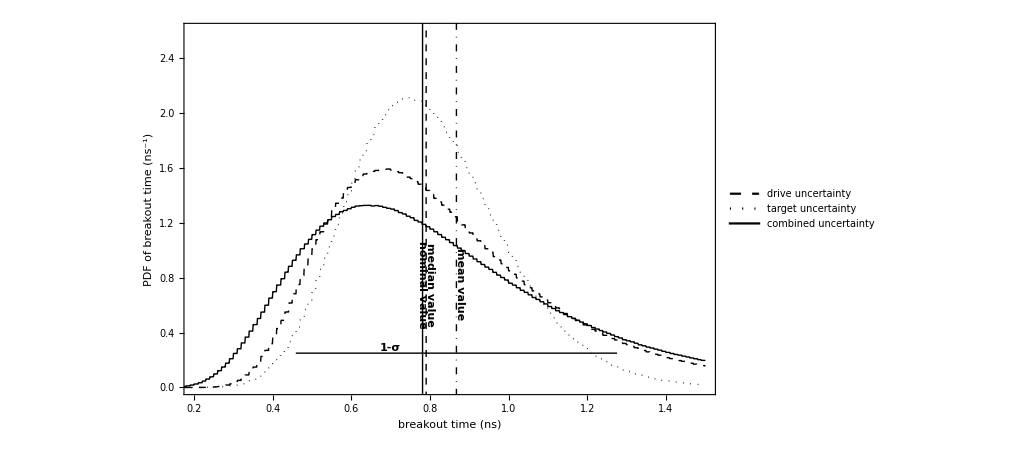

```mathematica
(DiscretePlot[{ #[ℋ,x]+shiftδ,#[ℋ2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[ℋ5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.2, 1.5},{0,2.6}},Epilog->{Black, Hline1, Text[Rotate[Style["median value",Black, Bold, Medium],-90 Degree],{medianH + .02,.75}],Black,DotDashed,Hline2,Text[Rotate[Style["mean value",Black,Bold,  Medium],-90 Degree],{meanH+.01,.75}],Black,Dashed, Hline3, Text[Rotate[Style["nominal value",Black, Bold, Medium],-90 Degree],{nominalH-.01,.75}], Black,Dashing[None], Hline5, Text[Style["1-σ",Black, Bold, Medium],{0.7,0.29}]}, PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["PDF of breakout time (ns^-1)", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{PDF})[[1]]
```

```mathematica
twentieth = InverseCDF[ℋ5N,0.2];
eightieth= InverseCDF[ℋ5N,0.8];
fiftieth = InverseCDF[ℋ5N,0.5];
nominalcdf = CDF[ℋ5N,nominal]
meancdf = CDF[ℋ5N,mean];
For[n =1,n<= 5, n++,Print[NumberForm[InverseCDF[ℋ5N,percentilelist[[n]]],6]," ", percentilelist[[n]]," percentile"]]
```

0.510876

0.547715 0.2 percentile

0.701153 0.4 percentile

0.780994 0.5 percentile

0.870961 0.6 percentile

1.12766 0.8 percentile

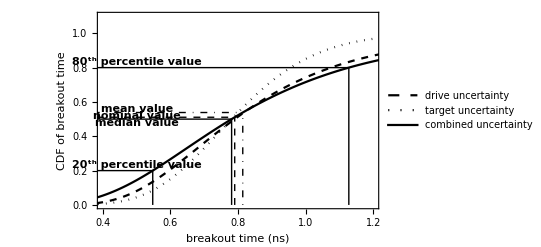

```mathematica
line7 = Line[{{0, 0.5}, {fiftieth, 0.5}}];
line8 = Line[{{fiftieth, 0.0}, {fiftieth, 0.5}}];
line9 = Line[{{0, 0.2}, {twentieth, 0.2}}];
line10 = Line[{{twentieth, 0.0}, {twentieth, 0.2}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line13 = Line[{{0, nominalcdf}, {nominal, nominalcdf}}];
line14 = Line[{{nominal, 0.0}, {nominal, nominalcdf}}];
line15 = Line[{{0, meancdf}, {mean, meancdf}}];
line16 = Line[{{mean, 0.0}, {mean, meancdf}}];
(DiscretePlot[{ #[ℋ,x]+shiftδ,#[ℋ2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[ℋ5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,1.1}}, Epilog->{line7, line8,line9,line10,line11,line12,Dashed, line13,Dashed, line14,DotDashed, line15,DotDashed,line16, Text[Style["median value",Black,Bold,  Medium],{0.5,0.48}], Text[Style["nominal value",Black,Bold,  Medium],{0.5,0.52}], Text[Style["mean value",Black,Bold,  Medium],{0.5,meancdf+0.02}], Text[Style["20^th percentile value",Black,Bold,  Medium],{0.5,0.23}], Text[Style["80^th percentile value",Black,Bold,  Medium],{0.5,0.83}]},PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["CDF of breakout time", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{CDF})[[1]]
```

```mathematica
(*Export["UQ_plots/histogramPDF_HE.pdf", plot3];
Export["UQ_plots/histogramCDF_HE.pdf", plot4];*)
```

## Temperature profile

```mathematica
(*Find min and max Subscript[ξ, max]*)
nm = 7/2;
xmaxmin =ξmaxn72 Sqrt[tval]/AAfunc[ AllPars,-1, 1, 1, 1];
xmaxmax =ξmaxn72 Sqrt[tval]/AAfunc[ AllPars,1, -1, -1, -1];
xlist = N@Subdivide[0,xmaxmax,Nevalpoints];
(*Export parameters to python code*)
AllParsCsv =  N[{T0val, ξmaxn72, κ0val, ρ0val,cv0val,pval* T0val,pval*κ0val, pval*ρ0val, pval*cv0val,omegaval, NPn, NHe, mh, tval, xmaxmax, Nevalpoints}];
Export["marshak_pars.csv", AllParsCsv];
```

0.986527

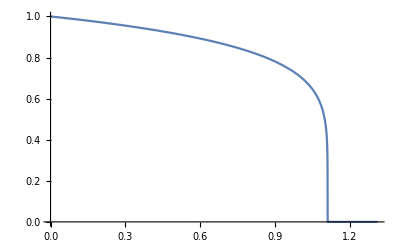

Import::noelem: The Import element "xi" is not present when importing as HDF5.

Import::noelem: The Import element "T" is not present when importing as HDF5.

```mathematica
(*Analytic T solutions*)
(*solve Marshak wave*)
(*load Marshak wave*)
marshakxi= Import["marshak_sol.hdf5",{"Datasets","xi"}];
marshakT= Import["marshak_sol.hdf5",{"Datasets","T"}];
interpolationlist = Table[0,{j,1, Length[marshakT]}];
For[it = 1, it<= Length[marshakT], it++,
interpolationlist[[it]] = {marshakxi[[it]], marshakT[[it]]};]
T = Interpolation[interpolationlist];
(*ICS[ξmax_, ξ_] := {T[ξmax]==1/5((nm+3)*ξmax*(-ξ+ξmax)/(nm+4))^(1/(nm+3)), u[ξmax]==-(((nm+3)/(nm+4))*ξmax)^(1/(nm+3))*1/(nm+3)*(ξmax-ξ)^((-2-nm)/(nm+3))1/5}
eqsMarshak = {D[T[ξ],ξ]==u[ξ], D[u[ξ],ξ] ==- u[ξ]*((T[ξ]^(-mh)*ξ)/(nm+4)+(nm+3)*T[ξ]^2*u[ξ])/(T[ξ]^3)} ;
bcs = {T[0]==1};
tol = 10^-7;
sol=NDSolve[{eqsMarshak,ICS[ξmaxn72,ξmaxn72-tol]},{T[ξ],u[ξ]},{ξ,0,ξmaxn72-tol},Method->{"Shooting","StartingInitialConditions"->{T[ξmaxn72]==ICS[ξmaxn72,ξmaxn72-tol][[1]],u[ξmaxn72]==ICS[ξmaxn72,ξmaxn72-tol][[2]]}}];*)
Clear[Tsol2]
(*Tsol2[ξξ_?NumericQ] :=Piecewise[{{((T[ξ]/.sol)/.ξ->ξξ )[[1]],0<=ξξ<=ξmaxn72},{0,True}}]*)
Tsol2[ξξ_?NumericQ] :=Piecewise[{{((T[ξ])/.ξ->ξξ ),0<=ξξ<=ξmaxn72},{0,True}}]
Plot[{ Tsol2[x]},{x,0,ξmaxn72 + 0.2}]
```

```mathematica
(*Import coefficients from python*)
AllPnCC= Import["coeffs_4d.hdf5",{"Datasets","all_Pn"}];
AllHeCC= Import["coeffs_4d.hdf5",{"Datasets","all_He"}];
(*DrivePnCC=Import["drive_coeffs_4d.hdf5",{"Datasets","drive_Pn"}];
DriveHeCC=Import["drive_coeffs_4d.hdf5",{"Datasets","drive_He"}];*)

(*TargetPnCC=Import["drive_coeffs_4d.hdf5",{"Datasets","target_Pn"}];*)
xlistpython = Import["drive_coeffs_4d.hdf5",{"Datasets","xlist"}];
Nevalpointspython = Length[xlistpython];
DrivePnExp = Table[{xlistpython[[nj]],1/2 DrivePnCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
DriveHeExp = Table[{xlistpython[[nj]],1/Sqrt[2 Pi] DriveHeCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
AllPnExp = Table[{xlistpython[[nj]],1/16 AllPnCC[[;;,1,1,1,1]][[nj]]},{nj,1,Length[xlistpython]}];
```

Import::general: No dataset associated with name all_He

Import::noelem: The Import element "all_He" is not present when importing as HDF5.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 2 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 3 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
(*Analytic moments*)
```

```mathematica
expectedAllPn = ParallelTable[{xlistpython[[ix]],Quiet[tempNthMomentPn[xlistpython[[ix]],tval, AllPars,1]]},{ix, 1, Nevalpointspython}];
(*expectedDrivePn2 = ParallelTable[{xlist[[ix]],(*Quiet[analyticProfileDriveUncertainty[xlist[[ix]],tval, DrivePars,1]]*)},{ix, 1, Nevalpoints}];*)
varianceAllPn = ParallelTable[{xlistpython[[ix]],Quiet[tempNthMomentPn[xlistpython[[ix]],tval, AllPars,2]-expectedAllPn[[ix,2]]^2]},{ix, 1, Nevalpointspython}];
stdAllPnp = Table[{xlistpython[[ix]],expectedAllPn[[ix,2]]+Sqrt[varianceAllPn[[ix,2]]] },{ix, 1, Nevalpointspython}];
stdAllPnm = Table[{xlistpython[[ix]], expectedAllPn[[ix,2]]-Sqrt[varianceAllPn[[ix,2]]]},{ix, 1, Nevalpointspython}];
expectedDrivePn = ParallelTable[{xlistpython[[ix]],Quiet[analyticProfileDriveUncertainty[xlistpython[[ix]],tval, DrivePars]]},{ix, 1, Nevalpointspython}];
expectedDriveHe = ParallelTable[{xlistpython[[ix]],Quiet[analyticprofileDriveHe[xlistpython[[ix]],tval, DrivePars]]},{ix, 1, Nevalpointspython}];
```

$Aborted

```mathematica
Print[RMSE[DrivePnExp[[;;,2]], expectedDrivePn[[;;,2]]], "RMSE DRIVE Pn"]
Print[RMSE[DriveHeExp[[;;,2]], expectedDriveHe[[;;,2]]], "RMSE DRIVE He"]
Print[RMSE[AllPnExp[[;;,2]], expectedAllPn[[;;,2]]], "RMSE ALL Pn"]
```

0.00102923RMSE DRIVE Pn

1/(5 √2)(√((-0.39868204802581+(Symbol[]⟦1⟧)/(√(2 π)))^2+(-0.39694124344324+(Symbol[]⟦2⟧)/(√(2 π)))^2+(-0.39514781189476+(Symbol[]⟦3⟧)/(√(2 π)))^2+(-0.39329838763615+(Symbol[]⟦4⟧)/(√(2 π)))^2+(-0.39138924126695+(Symbol[]⟦5⟧)/(√(2 π)))^2+(-0.38941622274709+(Symbol[]⟦6⟧)/(√(2 π)))^2+(-0.38737468777091+(Symbol[]⟦7⟧)/(√(2 π)))^2+(-0.38525940981665+(Symbol[]⟦8⟧)/(√(2 π)))^2+(-0.3830644652564+(Symbol[]⟦9⟧)/(√(2 π)))^2+(-0.38078309054849+(Symbol[]⟦10⟧)/(√(2 π)))^2+(-0.3784073637034+(Symbol[]⟦11⟧)/(√(2 π)))^2+(-0.37592843427023+(Symbol[]⟦12⟧)/(√(2 π)))^2+(-0.37333521988846+(Symbol[]⟦13⟧)/(√(2 π)))^2+(-0.37061309143602+(Symbol[]⟦14⟧)/(√(2 π)))^2+(-0.36774920211365+(Symbol[]⟦15⟧)/(√(2 π)))^2+(-0.36471094155899+(Symbol[]⟦16⟧)/(√(2 π)))^2+(-0.36147386264092+(Symbol[]⟦17⟧)/(√(2 π)))^2+(-0.35798849256903+(Symbol[]⟦18⟧)/(√(2 π)))^2+(-0.35419040564194+(Symbol[]⟦19⟧)/(√(2 π)))^2+(-0.34998614507708+(Symbol[]⟦20⟧)/(√(2 π)))^2+(-0.34524985574822+(Symbol[]⟦21⟧)/(√(2 π)))^2+(-0.33981930953185+(Symbol[]⟦22⟧)/(√(2 π)))^2+(-0.33350735536998+(Symbol[]⟦23⟧)/(√(2 π)))^2+(-0.32604617409582+(Symbol[]⟦24⟧)/(√(2 π)))^2+(-0.31723574461136+(Symbol[]⟦25⟧)/(√(2 π)))^2+(-0.30681349781662+(Symbol[]⟦26⟧)/(√(2 π)))^2+(-0.29462682424858+(Symbol[]⟦27⟧)/(√(2 π)))^2+(-0.28051627112592+(Symbol[]⟦28⟧)/(√(2 π)))^2+(-0.2644856605514+(Symbol[]⟦29⟧)/(√(2 π)))^2+(-0.24665498383435+(Symbol[]⟦30⟧)/(√(2 π)))^2+(-0.22725356620324+(Symbol[]⟦31⟧)/(√(2 π)))^2+(-0.20663171686501+(Symbol[]⟦32⟧)/(√(2 π)))^2+(-0.1852489906346+(Symbol[]⟦33⟧)/(√(2 π)))^2+(-0.16363250412298+(Symbol[]⟦34⟧)/(√(2 π)))^2+(-0.14231854715456+(Symbol[]⟦35⟧)/(√(2 π)))^2+(-0.12181336421243+(Symbol[]⟦36⟧)/(√(2 π)))^2+(-0.10257778231721+(Symbol[]⟦37⟧)/(√(2 π)))^2+(-0.084944566635729+(Symbol[]⟦38⟧)/(√(2 π)))^2+(-0.06917320394495+(Symbol[]⟦39⟧)/(√(2 π)))^2+(-0.055388114367551+(Symbol[]⟦40⟧)/(√(2 π)))^2+(-0.04359815941968+(Symbol[]⟦41⟧)/(√(2 π)))^2+(-0.033724361555409+(Symbol[]⟦42⟧)/(√(2 π)))^2+(-0.02567833503746+(Symbol[]⟦43⟧)/(√(2 π)))^2+(-0.019220275929689+(Symbol[]⟦44⟧)/(√(2 π)))^2+(-0.014145960686254+(Symbol[]⟦45⟧)/(√(2 π)))^2+(-0.010243569286005+(Symbol[]⟦46⟧)/(√(2 π)))^2+(-0.0073005600365435+(Symbol[]⟦47⟧)/(√(2 π)))^2+(-0.0051174235735443+(Symbol[]⟦48⟧)/(√(2 π)))^2+(-0.0035302992908453+(Symbol[]⟦49⟧)/(√(2 π)))^2+(-0.0023978223830904+(Symbol[]⟦50⟧)/(√(2 π)))^2))RMSE DRIVE He

0.285439RMSE ALL Pn

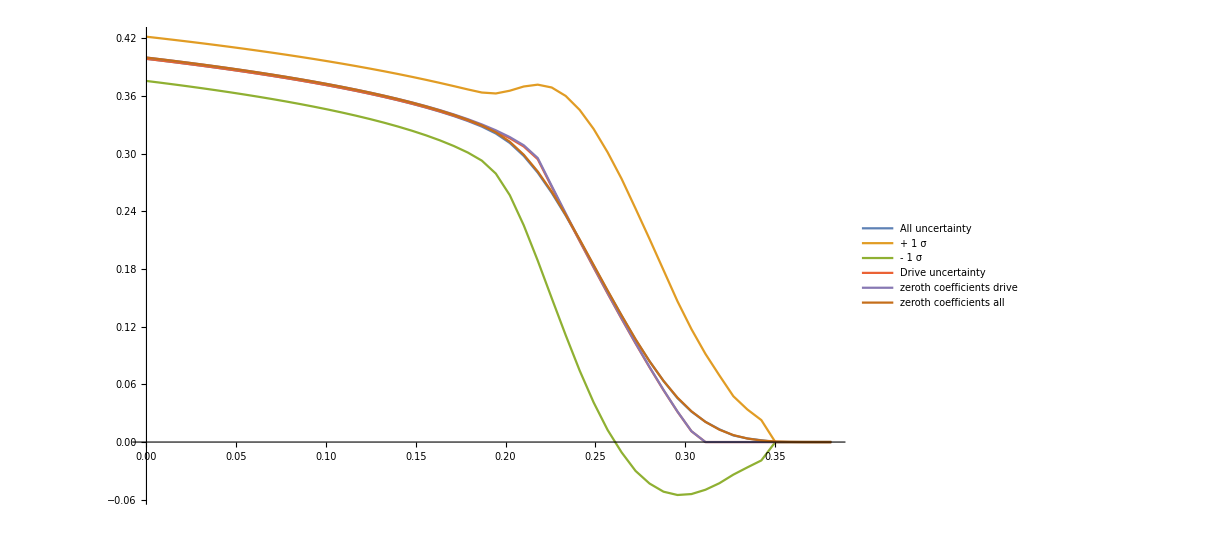

```mathematica
ListPlot[{expectedAllPn, stdAllPnp, stdAllPnm, expectedDrivePn,DrivePnExp,AllPnExp }, Joined->True, PlotLegends->{"All uncertainty", "+ 1 σ", "- 1 σ", "Drive uncertainty", "zeroth coefficients drive", "zeroth coefficients all"}]
```

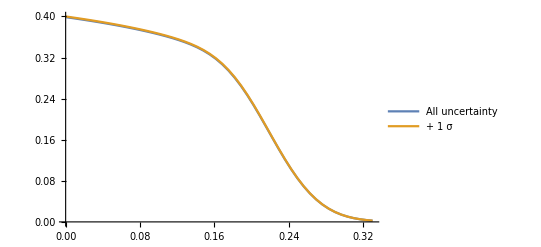

```mathematica
ListPlot[{expectedDriveHe, DriveHeExp }, Joined->True, PlotLegends->{"All uncertainty", "+ 1 σ", "- 1 σ", "Drive uncertainty", "zeroth coefficients drive", "zeroth coefficients all"}]
```

```mathematica
IntegrandFunc4[x_,t_,pars_, xx2_?NumericQ,xx3_?NumericQ, xx4_?NumericQ, l1_, l2_, l3_, l4_]:= NIntegrate[(IntegrandFunc2[x,t,pars, xx1, xx2,xx3, xx3]/.n->mh )𝒫4[xx1,xx2,xx3,xx4, l1-1,l2-1, l3-1,l4-1],{xx1, Max[-1,N[(-T0+((x^2*(cv+a4*xx4)*(a2*xx2+κ0)*(a3*xx3+ρ0)^2)/(t*ξmaxn72^2*ω^2))^(1/mh))/a1/.AllPars]],1},   AccuracyGoal->12];
𝒫4[θ1_,θ2_,θ3_,θ4_, l1_,l2_,l3_,l4_]:= Basis[l1,θ1] Basis[l2,θ2] Basis[l3,θ3] Basis[l4,θ4]
𝒞4[x_, t_, pars_, MM_] := ParallelTable[NIntegrate[(IntegrandFunc2[x,t,pars, xx1, xx2,xx3, xx3]/.n->mh )𝒫4[xx1,xx2,xx3,xx4, l1-1,l2-1, l3-1,l4-1],{xx1,-1,1},{xx2,-1,1},{xx3,-1,1},{xx4,-1,1},   AccuracyGoal->12],{l1,1, MM+1},{l2,1, MM+1},{l3,1, MM+1} ,{l4,1, MM+1}]
𝒞5[x_, t_, pars_, MM_] := ParallelTable[NIntegrate[IntegrandFunc4[x,t,pars, x2,x3, x4, l1, l2, l3, l4] ,{x2,-1,1},{x3,-1,1},{x4,-1,1},   AccuracyGoal->12],{l1,1, MM+1},{l2,1, MM+1},{l3,1, MM+1} ,{l4,1, MM+1}]
```

```mathematica
Max[-1,N[(-T0+((x^2*(cv+a4*xx4)*(a2*xx2+κ0)*(a3*xx3+ρ0)^2)/(t*ξmaxn72^2*ω^2))^(1/mh))/a1/.AllPars/.{xx2->0, xx3->0,xx4->0, t->tval, x->0.01}]]
```

-8.45082

```mathematica
𝒞5[0.01, tval, AllPars, 0]
```

{{{{6.34311}}}}

```mathematica
NIntegrate[IntegrandFunc4[0.01,tval,AllPars,x2,x3, x4, 1, 1, 1, 1],{x2, -1,1},{x3,-1,1},{x4,-1,1}]
```

6.34311

```mathematica
CCTABLE = Table[0, {j,1,Nevalpointspython}];
```

```mathematica
For[ix =1, ix<= Nevalpointspython, ix++,
Print[ix];
CCTABLE[[ix]]=𝒞4[xlistpython[[ix]], tval,AllPars, 1]]
```

1

2

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000207289 and 5.94573×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.80031×10^-7 and 2.96318×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.18223×10^-6 and 1.48643×10^-9 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.00673918,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.45008×10^-7 and 7.40795×10^-10 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.00673918,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

3

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000043612 and 1.48368×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.35414×10^-6 and 7.22139×10^-9 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000010903 and 3.70919×10^-9 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0134784,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.38535×10^-7 and 1.80535×10^-9 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0134784,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

4

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000068908 and 2.80231×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.3625×10^-6 and 1.40206×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000017227 and 7.00577×10^-9 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0202175,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.90625×10^-7 and 3.50516×10^-9 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0202175,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

5

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000969192 and 4.74246×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.65131×10^-6 and 2.42619×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000242298 and 1.18562×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0269567,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.12827×10^-7 and 6.06549×10^-9 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0269567,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

6

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000127993 and 7.52697×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.28453×10^-6 and 3.87815×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000319982 and 1.88174×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0336959,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.32113×10^-6 and 9.69538×10^-9 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0336959,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

7

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000162537 and 1.15446×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.33182×10^-6 and 5.88124×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000406342 and 2.88616×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0404351,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.83296×10^-6 and 1.47031×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0404351,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

8

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000201026 and 1.73395×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9.88498×10^-6 and 8.95961×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000502564 and 4.33487×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0471743,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.47124×10^-6 and 2.2399×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0471743,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

9

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000244023 and 2.56853×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000130574 and 1.3108×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000610056 and 6.42133×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0539135,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.26436×10^-6 and 3.27701×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0539135,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000292193 and 3.73912×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000169915 and 1.8748×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000730483 and 9.34781×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0606526,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.24788×10^-6 and 4.687×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0606526,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

11

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000346337 and 5.37138×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000218639 and 2.76824×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000865842 and 1.34284×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0673918,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.46598×10^-6 and 6.92059×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0673918,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

12

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000407408 and 7.53173×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000027904 and 3.96075×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000101852 and 1.88293×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.074131,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.97601×10^-6 and 9.90188×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.074131,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

13

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00047657 and 1.07146×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000354045 and 5.4821×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000119142 and 2.67866×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0808702,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8.85112×10^-6 and 1.37053×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0808702,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

14

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000555243 and 1.51766×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000447426 and 8.0215×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000138811 and 3.79414×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0876094,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000111856 and 2.00537×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0876094,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

15

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000645183 and 2.11559×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000564135 and 1.11755×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000161296 and 5.28898×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0943486,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000141034 and 2.79387×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0943486,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

16

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000748584 and 2.99665×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000710796 and 1.60638×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000187146 and 7.49163×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.101088,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000177699 and 4.01596×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.101088,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

17

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000868222 and 4.21752×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000896235 and 2.04036×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000217055 and 1.05438×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.107827,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000224059 and 5.10091×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.107827,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

18

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00100766 and 6.02268×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000113261 and 3.27793×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000251915 and 1.50567×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.114566,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000283154 and 8.19482×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.114566,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

19

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00117154 and 8.63197×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000143675 and 4.73296×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000292885 and 2.15799×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.121305,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000359187 and 1.18324×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.121305,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

20

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00136605 and 0.0000121654 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000183262 and 6.91484×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000341512 and 3.04136×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.128044,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000458155 and 1.72871×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.128044,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

21

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0015996 and 0.0000182565 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000235519 and 0.0000101283 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0003999 and 4.56411×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.134784,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000588798 and 2.53208×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.134784,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

22

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00188396 and 0.0000272007 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000305704 and 0.0000157281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000470989 and 6.80017×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.141523,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000764261 and 3.93202×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.141523,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

23

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00223618 and 0.0000413533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000402029 and 0.0000244095 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000559045 and 0.0000103383 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.148262,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000100507 and 6.10238×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.148262,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

24

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00268213 and 0.0000656173 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000537986 and 0.0000399808 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000670532 and 0.0000164043 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.155001,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000134497 and 9.99521×10^-6 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.155001,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

25

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00326331 and 0.00010219 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000737251 and 0.0000688679 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000815828 and 0.0000255474 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.16174,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000184313 and 0.000017217 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.16174,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

26

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00405385 and 0.000194881 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.00104571 and 0.000129942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00101346 and 0.0000487202 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.16848,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000261426 and 0.0000324854 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.16848,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

27

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0052059 and 0.000403623 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0015692 and 0.000285714 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.00130148 and 0.000100906 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.175219,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0003923 and 0.0000714285 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.175219,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

28

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.301692 and 1.89362×10^-6 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.106278 and 1.87996×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.075423 and 4.73406×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.181958,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0265694 and 4.6999×10^-7 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.181958,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.018949 and 1.83451×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0371748 and 1.72344×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.181958,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.181958,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

29

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.20126 and 0.0000604424 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.326668 and 0.0000559654 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.30031 and 0.0000151106 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.188697,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0816669 and 0.0000139914 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.188697,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.130807 and 0.0000529241 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0317715 and 0.000048479 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.188697,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.188697,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

30

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.372496 and 0.000229772 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5.07497 and 0.000306084 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0931239 and 0.0000574431 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.195436,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.26874 and 0.000076521 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.195436,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0587956 and 0.000172486 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.174648 and 0.000237601 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.195436,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.195436,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

31

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.441531 and 0.000303679 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.91023 and 0.000328039 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.110383 and 0.0000759197 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.202175,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.22756 and 0.0000820097 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.202175,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0975703 and 0.000210881 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.23874 and 0.000260669 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.202175,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.202175,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

32

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.70653 and 0.00105446 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.527227 and 0.000501259 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.17663 and 0.000263615 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.208915,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.131807 and 0.000125315 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.208915,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.316924 and 0.000407582 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.139153 and 0.000229217 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.208915,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.208915,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

33

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.46773 and 0.00333963 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.621245 and 0.00214309 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.155311 and 0.000535772 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.11693 and 0.000834907 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.215654,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.172615 and 0.00120187 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.399704 and 0.0019776 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.215654,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.215654,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

34

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.715439 and 0.00165091 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.1977 and 0.00291506 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.17886 and 0.000412728 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.222393,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.04942 and 0.000728765 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.222393,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.190998 and 0.00064599 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.479669 and 0.00113275 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.222393,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.222393,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

35

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.801318 and 0.00337069 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.90219 and 0.00516995 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.200329 and 0.000842671 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.229132,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.975548 and 0.00129249 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.229132,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.189988 and 0.000595213 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.551102 and 0.00136146 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.229132,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.229132,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

36

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.87273 and 0.00479597 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.58517 and 0.00974281 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.218183 and 0.00119899 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.235871,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.896292 and 0.0024357 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.235871,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.16679 and 0.000925971 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.609221 and 0.00266529 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.235871,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.235871,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

37

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.9329 and 0.00126101 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.2465 and 0.00565071 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.233225 and 0.000315252 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.242611,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.811626 and 0.00141268 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.242611,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.122617 and 0.000563617 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.652582 and 0.00198557 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.242611,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.242611,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

38

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.89836 and 0.0137826 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.954437 and 0.00528612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.724589 and 0.00344565 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.24935,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.238609 and 0.00132153 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.24935,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.678351 and 0.00353025 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0588678 and 0.00158457 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.24935,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.24935,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

39

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.953571 and 0.00402708 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.54229 and 0.00863542 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.238393 and 0.00100677 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.256089,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.635572 and 0.00215886 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.256089,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0172173 and 0.00169503 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.69082 and 0.00282384 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.256089,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.256089,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

40

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.920098 and 0.00150592 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.18662 and 0.00405724 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.230025 and 0.00037648 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.262828,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.546654 and 0.00101431 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.262828,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0968075 and 0.000798969 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.690976 and 0.0013373 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.262828,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.262828,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

41

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.857578 and 0.00166923 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.85481 and 0.00765613 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.214395 and 0.000417308 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.269567,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.463702 and 0.00191403 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.269567,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.167811 and 0.000842621 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.678602 and 0.00338287 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.269567,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.269567,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

42

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.779596 and 0.00407265 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.55064 and 0.0136395 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.194899 and 0.00101816 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.276306,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.38766 and 0.00340987 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.276306,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.220694 and 0.00251302 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.647361 and 0.00393412 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.276306,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.276306,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

43

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.27623 and 0.00654948 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.692384 and 0.00200838 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.319057 and 0.00163737 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.283046,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.173096 and 0.000502095 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.283046,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.599384 and 0.00378189 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.254703 and 0.00130314 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.283046,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.283046,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

44

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.03388 and 0.00386612 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.598658 and 0.00200409 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.258469 and 0.000966529 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.289785,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.149664 and 0.000501023 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.289785,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.541019 and 0.00129792 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.265704 and 0.000651423 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.289785,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.289785,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

45

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.509114 and 0.00782484 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.82659 and 0.0169725 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.127279 and 0.00195621 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.296524,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.206648 and 0.00424314 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.296524,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.260423 and 0.00254664 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.471476 and 0.00501963 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.296524,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.296524,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

46

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.421975 and 0.00606357 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.635321 and 0.00838859 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.105494 and 0.00151589 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.303263,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.15883 and 0.00209715 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.303263,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.24223 and 0.000875564 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.399105 and 0.00321652 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.303263,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.303263,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

47

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.333052 and 0.00218242 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.482906 and 0.0053859 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.083263 and 0.000545606 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.310002,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.120727 and 0.00134648 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.310002,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.213978 and 0.000943194 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.324486 and 0.00231694 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.310002,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.310002,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

48

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.261537 and 0.00104046 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.360876 and 0.00136036 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0653843 and 0.000260114 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.316742,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0902191 and 0.000340091 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.316742,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.179012 and 0.000539082 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.255454 and 0.000793494 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.316742,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.316742,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

49

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.194819 and 0.00210614 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0487047 and 0.000526534 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.323481,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.256058 and 0.00644817 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.141855 and 0.00116893 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.323481,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0640145 and 0.00161204 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.323481,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.191827 and 0.00356715 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.323481,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.323481,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

50

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.136526 and 0.00284408 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.171791 and 0.00612874 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0341315 and 0.00071102 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.33022,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0429478 and 0.00153218 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.33022,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.105111 and 0.0020306 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.33022,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.135137 and 0.00264278 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.33022,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.33022,0.6,{T0→0.4,ξ→1.11104,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

General::stop: Further output of NIntegrate::oidiv will be suppressed during this calculation.

```mathematica
CCTABLE/16
```

{{{{{0.398682}}}},{{{{0.397183}}}},{{{{0.395646}}}},{{{{0.394069}}}},{{{{0.392449}}}},{{{{0.390785}}}},{{{{0.389073}}}},{{{{0.38731}}}},{{{{0.385495}}}},{{{{0.383622}}}},{{{{0.381689}}}},{{{{0.37969}}}},{{{{0.377622}}}},{{{{0.375479}}}},{{{{0.373255}}}},{{{{0.370943}}}},{{{{0.368535}}}},{{{{0.366022}}}},{{{{0.363394}}}},{{{{0.360638}}}},{{{{0.35774}}}},{{{{0.354681}}}},{{{{0.351439}}}},{{{{0.347986}}}},{{{{0.344286}}}},{{{{0.340288}}}},{{{{0.335918}}}},{{{{0.33104}}}},{{{{0.325078}}}},{{{{0.317186}}}},{{{{0.306889}}}},{{{{0.294158}}}},{{{{0.279233}}}},{{{{0.262356}}}},{{{{0.243887}}}},{{{{0.224073}}}},{{{{0.202906}}}},{{{{0.181147}}}},{{{{0.158893}}}},{{{{0.136664}}}},{{{{0.115926}}}},{{{{0.096915}}}},{{{{0.0797642}}}},{{{{0.0646173}}}},{{{{0.0516619}}}},{{{{0.0397075}}}},{{{{0.0301816}}}},{{{{0.0225548}}}},{{{{0.0160036}}}},{{{{0.010737}}}}}